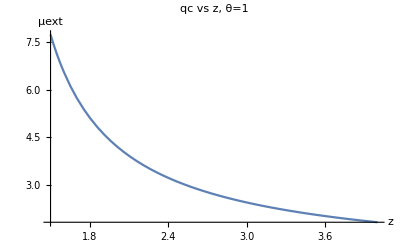

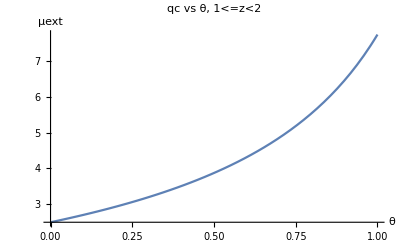

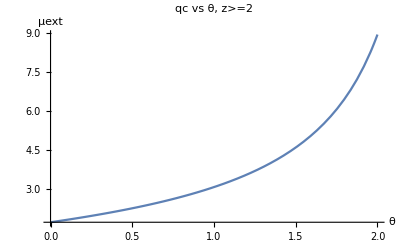

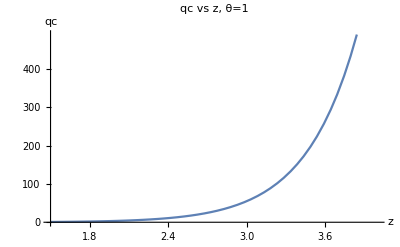

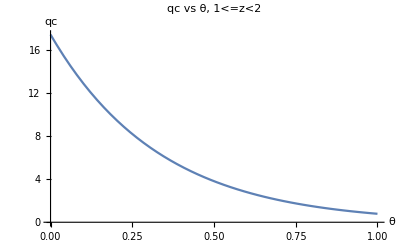

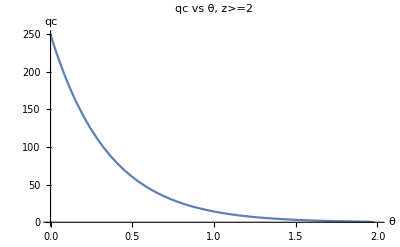

```mathematica
Block[
{f,μextremal,qcrit,ut,ut1},
f[u_,uh_,μ_,z_,θ_]:=1-(u/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ)(u^(2(z-θ+1))/uh^(2(z-θ)))(1-(u/uh)^(θ-z));
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ-z)Sqrt[f[us,uh,μ,z,θ]]/μ/(1-(us/uh)^(z-θ));
μextremal[uh_,z_,θ_]:=Sqrt[2(2+θ)(2+z-θ)]/(z-θ)/uh;
Print[Plot[μextremal[1,z,1],{z,1.5,4},AxesLabel->{z,μext},PlotLabel->"qc vs z, θ=1"]];
Print[Plot[μextremal[1,1.5,θ],{θ,0,1},AxesLabel->{θ,μext},PlotLabel->"qc vs θ, 1<=z<2"]];
Print[Plot[μextremal[1,2.5,θ],{θ,0,2},AxesLabel->{θ,μext},PlotLabel->"qc vs θ, z>=2"]];
Print[Plot[qcrit[0.1,1,0.75μextremal[1,z,1],z,1],{z,1.5,4},AxesLabel->{z,qc},PlotLabel->"qc vs z, θ=1"]];
Print[Plot[qcrit[0.1,1,0.75μextremal[1,1.5,θ],1.5,θ],{θ,0,1},AxesLabel->{θ,qc},PlotLabel->"qc vs θ, 1<=z<2"]];
Print[Plot[qcrit[0.1,1,0.75μextremal[1,2.5,θ],2.5,θ],{θ,0,2},AxesLabel->{θ,qc},PlotLabel->"qc vs θ, z>=2"]];
]
```